# ACM30100 - Mini-Project: Support Vectors

I began by  importing my data into Mathematica. In this case I’m analysing the quality of the coffee from 3 South American countries as scored by the Coffee Quality Institute.

```mathematica
data = SemanticImport["C:\\Users\\doher\\Documents\\GitHub\\mini-project-dohertycw\\merged_data_cleaned.csv"]
```

Dataset[<>]

I then chose to analyse the data based on three score indexes: Aroma, Flavor and the coffee’s total overall score. This was to see how they correlated.

```mathematica
dataCoffee=data[All,{4,21,22,31}]
```

Dataset[<>]

I then grouped by Country of Origin to enable me to extract the countries I wanted - in this case Brazil, Guatemala and Mexico. I chose these three for sample size.

```mathematica
Gdata = GroupBy[dataCoffee,Key["Country.of.Origin"]->KeyTake[{"Aroma","Flavor","Total.Cup.Points"}]]
```

Here I extracted my 3 country choices.

```mathematica
GdataSA = Gdata[[{2,3,10}]]
```

I then converted this data to a form most easily readable by mathematica and extracted values such that I could plot the different points.

```mathematica
NdataCoffee = Normal[GdataSA];
```

```mathematica
CoffeeDataSA = Values[NdataCoffee];
```

```mathematica
CoffeeDataSA2 = NdataCoffee;
```

```mathematica
ListPointPlot3D[CoffeeDataSA,PlotRange->Automatic]
```

-Graphics3D-

As we can see,  each country’s scoring by CQI is quite similar, so the data will probably be hard to separate using Support Vectors. Let’s check. 
First, let’s reduce this to a 2D plot for ease of analysis. I used Principal Component Analysis to reduce it’s dimensions.

```mathematica
dGdataSA = DimensionReduction[CoffeeDataSA[[All,1]],2, Method -> "PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
dGdataSAByType =dGdataSA/@GdataSA
```

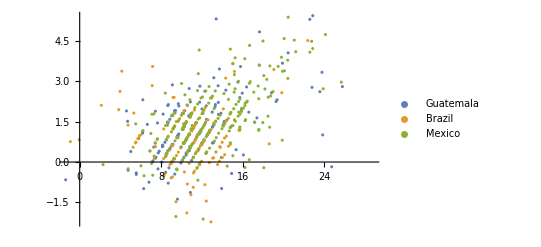

```mathematica
ListPlot[dGdataSAByType]
```

Seems not dissimilar to that of our 3D plot, including the data being quite intertwined. Let’s try Linear Fitting SVMs:

```mathematica
LinearFitting = Classify[Normal[dGdataSAByType], Method->{"SupportVectorMachine","KernelType"->"Linear"}]
```

ClassifierFunction[…]

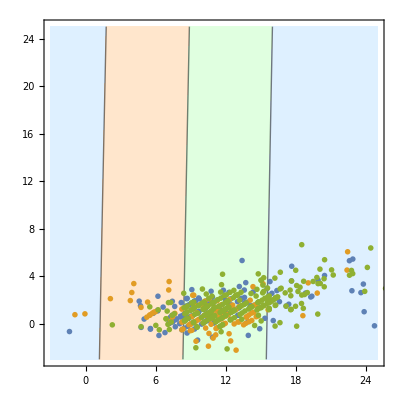

```mathematica
Show[ContourPlot[LinearFitting[{x,y},"Probability"->"Brazil"],{x,-3,25},{y,-3,25},Evaluated->False,ContourShading->{LightBlue,LightOrange,LightGreen},Contours->3],ListPlot[Values[dGdataSAByType],PlotMarkers->"OpenMarkers"]]
```

All things considered, not a terrible attempt! The Mexican coffee, represented by the green points, have their majority in the green section, so the SVMs are not incorrect to say that if it’s in the green half it’s probably Mexican. However, this doesn’t tell us much at all given that nearly all the points are in the green half, Guatemalan and Brazilian included. Let’s try a Polynomial Fit:

```mathematica
PolynomialFit=Classify[Normal[dGdataSAByType],Method->{"SupportVectorMachine","KernelType"->"Polynomial","GammaScalingParameter"->3}]
```

ClassifierFunction[…]

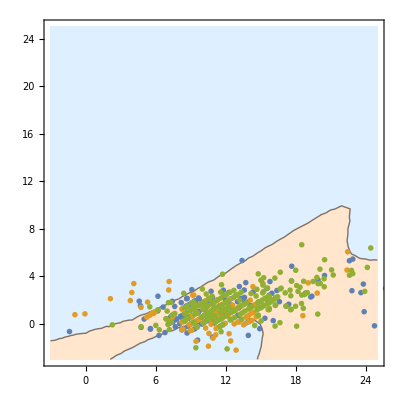

```mathematica
Show[ContourPlot[PolynomialFit[{x,y},"Probability"->"Mexico"],{x,-3,25},{y,-3,25},Evaluated->False,ContourShading->{LightBlue,LightOrange},Contours->{1/2}],ListPlot[Values[Normal[dGdataSAByType]],PlotMarkers->"OpenMarkers"]]
```

This does a better job and largely excludes the outlying Brazilian and Guatemalan points. However, it’s very overtrained, as we can see from the messy curve.  Let’s try a Gaussian function:

```mathematica
fR=Classify[Normal[dGdataSAByType],Method->{"SupportVectorMachine","KernelType"->"RadialBasisFunction","GammaScalingParameter"->1/(2 0.4^2)}]
```

ClassifierFunction[…]

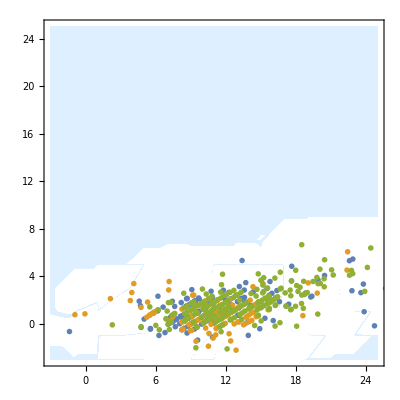

```mathematica
Show[ContourPlot[fR[{x,y},"Probability"->"Brazil"],{x,-3,25},{y,-3,25},Evaluated->False,ContourShading->{LightBlue,LightOrange},Contours->{1/2}],ListPlot[Values[dGdataSAByType],PlotMarkers->"OpenMarkers"]]
```

This has failed entirely! Extremely overtrained and not quite making sense. I would say overall, if one was to use SVMs for this, that the polynomial case would be best. However given how entagled the points are, it may be hard to determine this with SVMs.